Linearyzacja dynamiczna

```mathematica
loadNotebook["uproszczony_off_9_model.nb"];
```

```mathematica
wyliczSterowanie[wd_,w_,k1_,k2_]:=(
eta={Subscript[η, 1][t],Subscript[η, 2][t],Subscript[η, 3][t],Subscript[η, 4][t],Subscript[η, 5][t]};
uklad=Transpose[G2u.Transpose[{{Subscript[η, 1][t],Subscript[η, 2][t],Subscript[η, 3][t],Subscript[η, 4][t],Subscript[η, 5][t]}}]][[1]];
podstawienie= {D[x[t],t]->uklad[[1]],D[y[t],t]->uklad[[2]],D[Subscript[θ, 0][t],t]->uklad[[3]], D[Subscript[θ, u1][t],t]->uklad[[4]],D[Subscript[ϕ, u1][t],t]->uklad[[5]],D[Subscript[θ, u2][t],t]->uklad[[6]],D[Subscript[ϕ, u2][t],t]->uklad[[7]],D[Subscript[r, 1][t],t]->uklad[[8]],D[Subscript[r, 2][t],t]->uklad[[9]]};
wp=D[w,t] /. podstawienie;
wpp=D[wp,t]/.podstawienie;
dcoe={Coefficient[wpp,D[Subscript[η, 1][t],t]],Coefficient[wpp,D[Subscript[η, 2][t],t]],Coefficient[wpp,D[Subscript[η, 3][t],t]],Coefficient[wpp,D[Subscript[η, 4][t],t]],Coefficient[wpp,D[Subscript[η, 5][t],t]]} // Simplify;
coe={Coefficient[wpp,Subscript[η, 1][t]],Coefficient[wpp,Subscript[η, 2][t]],Coefficient[wpp,Subscript[η, 3][t]],Coefficient[wpp,Subscript[η, 4][t]],Coefficient[wpp,Subscript[η, 5][t]]} // Simplify;
test = dcoe//Simplify;
test={ToString[test[[1]]]=="{0, 0, 0, 0, 0}",ToString[test[[2]]]=="{0, 0, 0, 0, 0}",ToString[test[[3]]]=="{0, 0, 0, 0, 0}",ToString[test[[4]]]=="{0, 0, 0, 0, 0}",ToString[test[[5]]]=="{0, 0, 0, 0, 0}"};
Kdd={If[test[[1]],coe[[1]],dcoe[[1]]],If[test[[2]],coe[[2]],dcoe[[2]]],If[test[[3]],coe[[3]],dcoe[[3]]],If[test[[4]],coe[[4]],dcoe[[4]]],If[test[[5]],coe[[5]],dcoe[[5]]]} // Transpose;
Det[Kdd] // Simplify //Print;
P =wpp-Kdd.Table[If[test[[i]],eta[[i]],D[eta[[i]],t]],{i,{1,2,3,4,5}}] // Simplify;
K1 = k1*IdentityMatrix[5];
K2 = k2*IdentityMatrix[5];
sterowanie=Inverse[Kdd].(-P+D[D[wd,t],t]-K1.(D[w,t]-D[wd,t])-K2.(w-wd)) /. {l-> 0.1};
{test,sterowanie}
);

rozwiazRownania[sterowanie_,test_,q0_,tmax_]:=(
pstrona = Transpose[G2u.Transpose[{ηu[t]}]][[1]];
lstrona = D[qu[t],t];
sterbez={};
q01={};
For[j=1,j<6,j++,If[test[[j]],AppendTo[sterbez,eta[[j]]->sterowanie[[j]]];,lstrona=Join[lstrona,{D[eta[[j]],t]}];
pstrona=Join[pstrona,{sterowanie[[j]]}];
AppendTo[q01,(eta[[j]]/.{t->0})==0.01];]];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.sterbez~Join~{l-> 0.1}) ~Join~ q0~Join~q01;
rozwiazanieu = NDSolve[tosolve, {x,y,Subscript[θ, 0],Subscript[θ, u1],Subscript[ϕ, u1],Subscript[θ, u2],Subscript[ϕ, u2],Subscript[r, 1],Subscript[r, 2]}, {t,0,tmax}, Method->Automatic, MaxSteps->1000000];
rozwiazanieu
);

wyrysuj[rozwiazanieu_, w_,wd_,tmax_,anim_]:=Module[{},
Plot[w[[1]]-wd[[1]]/.rozwiazanieu,{t,0,tmax}, PlotRange->All, AxesLabel->{"t","ex"}] //Print;
Plot[w[[2]]-wd[[2]]/.rozwiazanieu,{t,0,tmax}, PlotRange->All, AxesLabel->{"t","ey"}] //Print;
Plot[Evaluate[{Subscript[θ, u1][t],  Subscript[θ, u2][t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","skrecenie"}, PlotStyle->{Red, Blue}, PlotLegends->{"θ_u1",  "θ_u2"}] //Print;
Plot[Evaluate[{Subscript[ϕ, u1]'[t],  Subscript[ϕ, u2]'[t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","predkosc"},PlotStyle->{Red, Blue}, PlotLegends->{"ϕ_u1",  "ϕ_u2"}] //Print;
Plot[Evaluate[{Subscript[r, 1][t],  Subscript[r, 2][t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","r"},PlotStyle->{Red, Blue}, PlotLegends->{"r_1",  "r_2"}] //Print;

krzywa1u[t_] = {x[t] ,y[t]} /. rozwiazanieu;

xu[t_] = (x[t]/.rozwiazanieu)[[1]]  ;
yu[t_] = (y[t]/.rozwiazanieu)[[1]]  ;

x1u[t_] = ((x[t]+l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
y1u[t_] = ((y[t]-l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
krzywasu[t_] = ({x1u[t], y1u[t]} /. rozwiazanieu);

x2u[t_] = ((x[t]+2l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
y2u[t_] = ((y[t]-2l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
krzywa2u[t_] = ({x2u[t], y2u[t]}/. rozwiazanieu);

xpu[t_] = (x1u'[t] /.rozwiazanieu)[[1]];
ypu[t_] = (y1u'[t] /. rozwiazanieu)[[1]];
vu[t_] = Re[Sqrt[(xpu[t])^2+(ypu[t])^2]];

krzywadu[t_]={xd[t],yd[t]};

ParametricPlot[{krzywadu[t],krzywa1u[t], krzywa2u[t], krzywasu[t]},{t,0,1tmax},PlotStyle->{{Black,Thick},Blue,Green,Red}] // Print;

a1=Animate[
Show[
{Plot[vu[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,vu[t]}]]}]
}
],
{t,0,tmax}];

curvsu = ParametricPlot[{krzywasu[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Red];
curv1u = ParametricPlot[{krzywa1u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Blue];
curv2u = ParametricPlot[{krzywa2u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Yellow];
curvd = ParametricPlot[{xd[t],yd[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Black];
ParametricPlot[{krzywa1u[t],krzywadu[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}] // Print;
p1x[t_]=((x[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p1y[t_]=((y[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2x[t_]=((x[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2y[t_]=((y[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p3x[t_]=((x2u[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p3y[t_]=((y2u[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4x[t_]=((x2u[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4y[t_]=((y2u[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
a2=Animate[
Show[
{curvsu, curv1u, curv2u , curvd},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{x1u[t],y1u[t]}]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.006],Green,
Line[
{
Dynamic[{xu[t],yu[t]}],
Dynamic[{x2u[t],y2u[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Red,
Line[
{
Dynamic[{p1x[t],p1y[t]}],
Dynamic[{p2x[t],p2y[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Red,
Line[
{
Dynamic[{p3x[t],p3y[t]}],
Dynamic[{p4x[t],p4y[t]}]
}
]
}]
}
],
{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

-(Csc[θ_u2[t]] Sin[θ_u1[t]] r_1[t]^2 η_2[t]^3)/r_2[t]^2

(True
False
False
True
True)

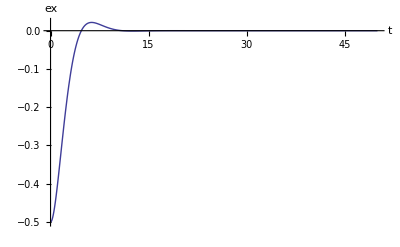

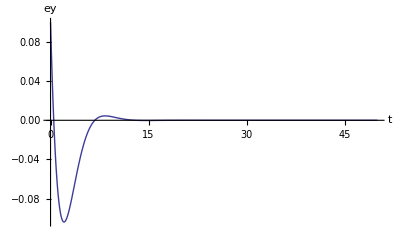

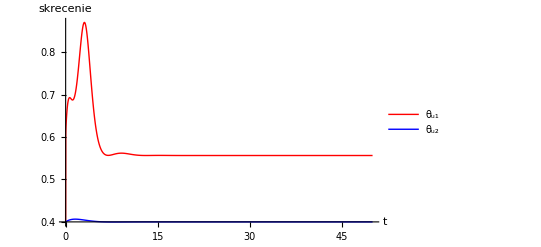

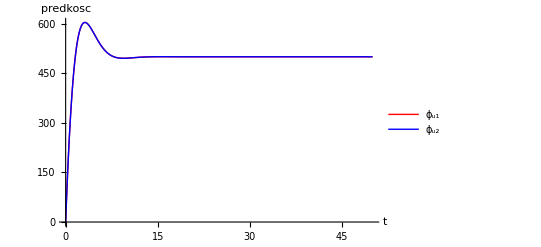

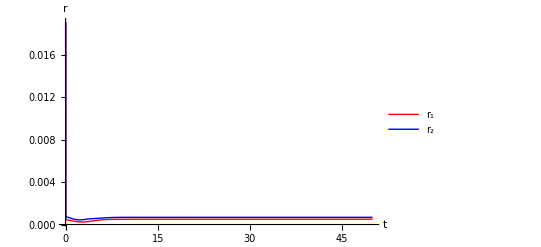

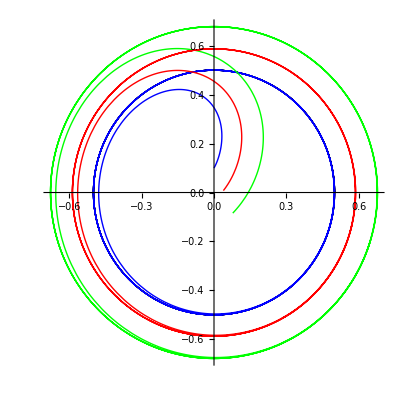

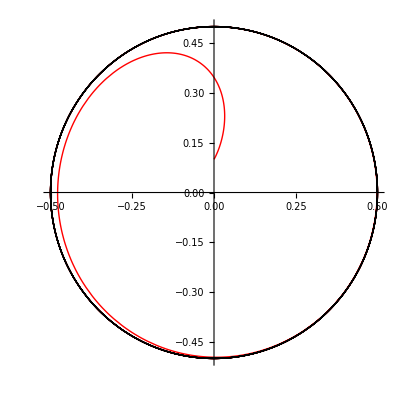

```mathematica
{xd[t_],yd[t_]}=kolo[t,0.5,2];
td[t_]=0.4;
h={x[t],y[t],Subscript[θ, u2][t],Subscript[ϕ, u1][t],Subscript[ϕ, u2][t]};
hd={xd[t],yd[t],td[t],wirowanie*t,wirowanie*t};
{test,sterowanie}=wyliczSterowanie[hd,h,1,0.5];
tmax=50;
test//MatrixForm
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0.4, Subscript[θ, u1][0]==0.4, Subscript[ϕ, u1][0]==0, Subscript[θ, u2][0]== 0.4, Subscript[ϕ, u2][0]==0.4,Subscript[r, 1][0]==0.02,Subscript[r, 2][0]==0.02(*,WhenEvent[Subscript[θ, u2][t]>1.4,Subscript[θ, u2][t]->1.35],WhenEvent[Subscript[θ, u1][t]>1.4,Subscript[θ, u1][t]->1.35]*)};
rozwiazanieu=rozwiazRownania[sterowanie,test,q0,tmax];
wyrysuj[rozwiazanieu,h,hd,tmax,True];
```

```mathematica
tmax = 50;
td[t_]=0.4;
d = 0.0;
w={x[t]+d*Cos[Subscript[θ, u1][t]+Subscript[θ, 0][t]],y[t]+d*Sin[Subscript[θ, u1][t]+Subscript[θ, 0][t]],Subscript[θ, u2][t]};(*Cos[Subscript[θ, u2][t]]+Cot[Subscript[θ, u1][t]]Sin[Subscript[θ, u2][t]]*)
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==-0.0, Subscript[θ, u1][0]==0.4, Subscript[ϕ, u1][0]==0, Subscript[θ, u2][0]== 0.4, Subscript[ϕ, u2][0]==0};

For[i=0,i<4,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,4,10]];
wd={xd[t],yd[t],td[t]};
{test,sterowanie}=wyliczSterowanie[wd,w,1,0.5];
rozwiazanieu=rozwiazRownania[sterowanie,test,q0,tmax];
wyrysuj[rozwiazanieu,w,wd,tmax,False];
];
```

0

Det::matsq: Argument {{0, Cos[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, Sin[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}} at position 1 is not a non-empty square matrix.

Det[{{0,Cos[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,Sin[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,0,1,0,0}}]

Inverse::matsq: Argument {{0, Cos[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, Sin[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}} at position 1 is not a non-empty square matrix.

Dot::dotsh: Tensors {{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}} and {-1/2\ Cos[t/2] + Derivative[1][x][t], Sin[π/4 + t] + Derivative[1][y][t], Derivative[1][θ_u2][t]} have incompatible shapes.

Dot::dotsh: Tensors {{0.5, 0., 0., 0., 0.}, {0., 0.5, 0., 0., 0.}, {0., 0., 0.5, 0., 0.}, {0., 0., 0., 0.5, 0.}, {0., 0., 0., 0., 0.5}} and {0.  - Sin[t/2] + x[t], 0.  - Cos[π/4 + t] + y[t], -0.4 + θ_u2[t]} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 3 of Inverse[{{0, Cos[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, Sin[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}}] . {« 1 »} does not exist.

Part::partw: Part 4 of Inverse[{{0, Cos[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, Sin[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}}] . {« 1 »} does not exist.

Part::partw: Part 5 of Inverse[{{0, Cos[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, Sin[Subscript[« 2 »][« 1 »] + Subscript[« 2 »][« 1 »]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}}] . {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Inverse::matsq: Argument {{0, Cos[TemporaryVariable$37702[t] + TemporaryVariable$37703[t]]\ TemporaryVariable$37695[t], 0, 0, 0}, {0, Sin[TemporaryVariable$37702[t] + TemporaryVariable$37703[t]]\ TemporaryVariable$37695[t], 0, 0, 0}, {0, 0, 1, 0, 0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse :: matsq will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

1

Det::matsq: Argument {{0, Cos[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, Sin[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}} at position 1 is not a non-empty square matrix.

Det[{{0,Cos[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,Sin[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,0,1,0,0}}]

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

2

Det::matsq: Argument {{0, Cos[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, Sin[θ_0[t] + θ_u1[t]]\ r_1[t], 0, 0, 0}, {0, 0, 1, 0, 0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Det :: matsq will be suppressed during this calculation.

Det[{{0,Cos[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,Sin[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,0,1,0,0}}]

NDSolve::ndsdtc: The time constraint of 1. seconds was exceeded trying to solve for derivatives, so the system will be treated as a system of differential-algebraic equations. You can use Method->{"EquationSimplification"->"Solve"} to have the system solved as ordinary differential equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

General::stop: Further output of NDSolve :: icfail will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

3

Det[{{0,Cos[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,Sin[θ_0[t]+θ_u1[t]] r_1[t],0,0,0},{0,0,1,0,0}}]

NDSolve::ndsdtc: The time constraint of 1. seconds was exceeded trying to solve for derivatives, so the system will be treated as a system of differential-algebraic equations. You can use Method->{"EquationSimplification"->"Solve"} to have the system solved as ordinary differential equations.

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»